```mathematica
(*Final*)
```

```mathematica
(* ---------------- vars ----------------*)
nVars=0;
GetKE[Gb_,Vb_]:=(1/2*Transpose[Vb].Gb.Vb)[[1,1]];
GetPE[m_,T_]:=m*g*T[[2,4]];
qs={};
qsvars={};
qsInit={};
dqsInit={};
(* ------------ objects ----------------- *)
nObjects=0;
objNames={};
(* Properties *)
masses={};
inertias={};
lens={};
g=9.8;
(* Transformation matrices *)
Ts={};
pFronts={};
pBacks={};

(* Vertices for impact detection *)
impObjVertexs={};
impObjVertexGroupIDs={};
(* Edges for impact detection *)
impObjEdges={};
impObjEdgeGroupIDs={};
```

```mathematica
(* ------------ Create objects ----------------- *)

CreateOneLink[linkgeometry_,options_]:=Module[{l,T,pFront,pBack},
nObjects=nObjects+1;
If[options=="BaseLink",(
{{p1x,p1y},{p2x,p2y}}=linkgeometry;
l=CalcDist[p1x,p1y,p2x,p2y];
objqsinit={(p1x+p2x)/2,(p1y+p2y)/2,myArcTan[p1x,p1y,p2x,p2y]};

(*Vars*)
nDOF=3;
{objqs,objqsvars}=pushVars[nDOF];
x=objqs[[1]];
y=objqs[[2]];
θ=objqs[[3]];
{T,pFront,pBack}=CalcAndPushT[x,y,θ,l];

qsInit=Join[qsInit,objqsinit];
dqsInit=Join[dqsInit,ConstantArray[0,nDOF]];

(*Impact*)
PushVertex[pFront,nthGroup];
PushVertex[pBack,nthGroup];

PushEdge[{pFront[[1;;2,1]],pBack[[1;;2,1]]},nthGroup];
)];
If[options=="AppendLink",(
{{p1x,p1y},{p2x,p2y}}=linkgeometry;
l=CalcDist[p1x,p1y,p2x,p2y];
)];
If[options=="Wall",(
{{p1x,p1y},{p2x,p2y}}=linkgeometry;
l=CalcDist[p1x,p1y,p2x,p2y];
x=(p1x+p2x)/2;
y=(p1y+p2y)/2;
θ=myArcTan[p1x,p1y,p2x,p2y];
{T,pFront,pBack}=CalcAndPushT[x,y,θ,l];

PushVertex[pFront,nthGroup];
PushVertex[pBack,nthGroup];
PushEdge[linkgeometry,nthGroup];
)];

(* --------------------------------------- *)
(* mass and inertia*)
mass=lToMass[l];
inertia=lToInertia[l];
AppendTo[masses,mass];
AppendTo[inertias,inertia];
AppendTo[lens,l];
(*Return*)
{T,pFront,pBack}
]


nthGroup=1;
{T1,pFront1,pBack1}=CreateOneLink[{{-0.5,-0.5},{0.5,0.5}},"BaseLink"];

nthGroup=10;
{T2,pFront2,pBack2}=CreateOneLink[{{-2,-0.6},{+2,-0.6}},"Wall"];
T1
T2
```

{{Cos[$q3[t]],-Sin[$q3[t]],0,$q1[t]},{Sin[$q3[t]],Cos[$q3[t]],0,$q2[t]},{0,0,1,0},{0,0,0,1}}

{{1.,0.,0.,0.},{0.,1.,0.,-0.6},{0.,0.,1.,0.},{0.,0.,0.,1.}}

```mathematica
(* Prepare *)
dqs=D[qs,t];
ddqs=D[dqs,t];
```

```mathematica
(* --------------- Left side of EL eqs -------------- *)
(* Body generalized mass, composed of Inertia Tensor and Mass Matrix *)
getGb[j_,m_]:=ArrayFlatten[({{DiagonalMatrix[{j,j,j}], Zeros[3,3]}, {Zeros[3,3], DiagonalMatrix[{m,m,m}]}})]
Gbs=Table[getGb[inertias[[i]],masses[[i]]],{i,1,nObjects}]//Simplify;
(* Body screw axis *)
Vbs=Table[GenUnhat[InvT[Ts[[i]]].D[Ts[[i]],t]],{i,1,nObjects}]//Simplify;
(* Lagrange Equations: Kinetic and Potential Energy *)
GetKE[Gb_,Vb_]:=(1/2*Transpose[Vb].Gb.Vb)[[1,1]];
GetPE[m_,T_]:=m*g*T[[2,4]];
KEs=Table[GetKE[Gbs[[i]],Vbs[[i]]],{i,1,nObjects}]//Simplify;
PEs=Table[GetPE[masses[[i]],Ts[[i]]],{i,1,nObjects}]//Simplify;
Lag=Simplify[Total[Join[KEs,-PEs]],qs∈Reals];
(* Left side of Euler-Lagrange Equations*)
ELeqsLeft=Simplify[D[D[Lag,{dqs}],t]-D[Lag,{qs}],qs∈Reals];
```

```mathematica
(* --------------- Right side of EL eqs -------------- *)
(* Constraints *)
(*
conslink1P1x=p1Ends[[1]][[2,1]];(* y=0 *)
conslink1P1y=p1Ends[[2]][[2,1]];(* y=0 *)
*)
cons=Simplify[{},qs∈Reals];
nCons=Length[cons];
If[nCons>0,
(λs=Transpose[{Table[Symbol["$λ"<>ToString@i],{i,nCons}]}];
consgrad=Transpose[Grad[cons,qs]]; (* Grad[2,5]->Mat(2,5),Transpose->(5,2)*)
consddt=Simplify[D[D[cons,t],t],qs∈Reals])];
```

```mathematica
(* External forces *)
externalForces=ConstantArray[0,nVars];
```

```mathematica
(* ----------------------------- *)
(* Solve *)
If[nCons>0,(* with constraints *)
(EulerLagEqs=Thread[ELeqsLeft==Flatten[consgrad.λs]+externalForces]//Simplify;
consddtEqs=TurnToEq[consddt,ConstantArray[0,nCons]];
EQ=Solve[Join[EulerLagEqs,consddtEqs],Join[ddqs,Flatten[λs]]]),
(* No constraint *)
EulerLagEqs=Simplify[TurnToEq[ELeqsLeft,externalForces],qs∈Reals];
EQ=Solve[EulerLagEqs,ddqs]];
```

```mathematica
(* ----------------------------- *)
(* Preprae for NDSolve *)
timeend=0.3;
MAXIMPACTTIMES=30;
impactDetectionError=0.05;
intergrationMaxStepSize=0.001;
ifprint=True;

SetUpImpacts[]
ddqSolve=TurnToEq[ddqs,EQ[[1,;;,2]]];

(* NDsolve *)
{end,data,bounces}=BouncingBall[qsInit,dqsInit];
```

dis curr:{-4.4,-0.4,-1.86777,0.96066}, prev:{-4.4,-0.4,-1.86777,0.96066}

pre*dis:{19.36,0.16,3.48855,0.922868},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.4,-0.4,-1.86777,0.96066}, prev:{-4.4,-0.4,-1.86777,0.96066}

pre*dis:{19.36,0.16,3.48855,0.922868},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.4,-0.4,-1.86777,0.96066}, prev:{-4.4,-0.4,-1.86777,0.96066}

pre*dis:{19.36,0.16,3.48855,0.922868},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.4,-0.4,-1.86777,0.96066}, prev:{-4.4,-0.4,-1.86777,0.96066}

pre*dis:{19.36,0.16,3.48855,0.922868},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.4,-0.4,-1.86777,0.96066}, prev:{-4.4,-0.4,-1.86777,0.96066}

pre*dis:{19.36,0.16,3.48855,0.922868},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.4,-0.4,-1.86777,0.96066}, prev:{-4.4,-0.4,-1.86777,0.96066}

pre*dis:{19.36,0.16,3.48855,0.922868},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.4,-0.4,-1.86777,0.96066}, prev:{-4.4,-0.4,-1.86777,0.96066}

pre*dis:{19.36,0.16,3.48855,0.922868},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39998,-0.399979,-1.86776,0.960665}, prev:{-4.39998,-0.399979,-1.86776,0.960665}

pre*dis:{19.3598,0.159983,3.48853,0.922878},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39992,-0.399918,-1.86775,0.960681}, prev:{-4.39992,-0.399918,-1.86775,0.960681}

pre*dis:{19.3593,0.159935,3.48848,0.922907},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39982,-0.399819,-1.86772,0.960705}, prev:{-4.39982,-0.399819,-1.86772,0.960705}

pre*dis:{19.3584,0.159855,3.48838,0.922955},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39968,-0.39968,-1.86769,0.96074}, prev:{-4.39968,-0.39968,-1.86769,0.96074}

pre*dis:{19.3572,0.159744,3.48825,0.923022},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.3995,-0.399502,-1.86764,0.960785}, prev:{-4.3995,-0.399502,-1.86764,0.960785}

pre*dis:{19.3556,0.159602,3.48809,0.923107},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39929,-0.399285,-1.86759,0.960839}, prev:{-4.39929,-0.399285,-1.86759,0.960839}

pre*dis:{19.3537,0.159429,3.48789,0.923211},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39903,-0.399029,-1.86752,0.960903}, prev:{-4.39903,-0.399029,-1.86752,0.960903}

pre*dis:{19.3515,0.159224,3.48765,0.923335},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39873,-0.398733,-1.86745,0.960977}, prev:{-4.39873,-0.398733,-1.86745,0.960977}

pre*dis:{19.3489,0.158988,3.48737,0.923477},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.3984,-0.398398,-1.86737,0.961061}, prev:{-4.3984,-0.398398,-1.86737,0.961061}

pre*dis:{19.3459,0.158721,3.48706,0.923637},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39802,-0.398025,-1.86727,0.961154}, prev:{-4.39802,-0.398025,-1.86727,0.961154}

pre*dis:{19.3426,0.158424,3.48671,0.923817},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39761,-0.397611,-1.86717,0.961257}, prev:{-4.39761,-0.397611,-1.86717,0.961257}

pre*dis:{19.339,0.158095,3.48632,0.924016},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39716,-0.397159,-1.86706,0.96137}, prev:{-4.39716,-0.397159,-1.86706,0.96137}

pre*dis:{19.335,0.157735,3.4859,0.924233},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39667,-0.396667,-1.86693,0.961493}, prev:{-4.39667,-0.396667,-1.86693,0.961493}

pre*dis:{19.3307,0.157345,3.48544,0.924469},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39614,-0.396137,-1.8668,0.961626}, prev:{-4.39614,-0.396137,-1.8668,0.961626}

pre*dis:{19.326,0.156924,3.48495,0.924725},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39557,-0.395567,-1.86666,0.961768}, prev:{-4.39557,-0.395567,-1.86666,0.961768}

pre*dis:{19.321,0.156473,3.48441,0.924999},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39496,-0.394958,-1.86651,0.961921}, prev:{-4.39496,-0.394958,-1.86651,0.961921}

pre*dis:{19.3157,0.155992,3.48385,0.925292},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39431,-0.394309,-1.86634,0.962083}, prev:{-4.39431,-0.394309,-1.86634,0.962083}

pre*dis:{19.31,0.15548,3.48324,0.925603},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39362,-0.393622,-1.86617,0.962255}, prev:{-4.39362,-0.393622,-1.86617,0.962255}

pre*dis:{19.3039,0.154938,3.4826,0.925934},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39289,-0.392895,-1.86599,0.962436}, prev:{-4.39289,-0.392895,-1.86599,0.962436}

pre*dis:{19.2975,0.154366,3.48192,0.926284},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39213,-0.392129,-1.8658,0.962628}, prev:{-4.39213,-0.392129,-1.8658,0.962628}

pre*dis:{19.2908,0.153765,3.48121,0.926652},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39132,-0.391324,-1.8656,0.962829}, prev:{-4.39132,-0.391324,-1.8656,0.962829}

pre*dis:{19.2837,0.153134,3.48046,0.92704},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.39048,-0.39048,-1.86539,0.96304}, prev:{-4.39048,-0.39048,-1.86539,0.96304}

pre*dis:{19.2763,0.152474,3.47967,0.927447},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.3896,-0.389596,-1.86517,0.963261}, prev:{-4.3896,-0.389596,-1.86517,0.963261}

pre*dis:{19.2686,0.151785,3.47884,0.927872},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.38867,-0.388673,-1.86494,0.963492}, prev:{-4.38867,-0.388673,-1.86494,0.963492}

pre*dis:{19.2605,0.151067,3.47798,0.928317},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.38771,-0.387711,-1.86469,0.963732}, prev:{-4.38771,-0.387711,-1.86469,0.963732}

pre*dis:{19.252,0.15032,3.47709,0.92878},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.38671,-0.38671,-1.86444,0.963983}, prev:{-4.38671,-0.38671,-1.86444,0.963983}

pre*dis:{19.2432,0.149545,3.47615,0.929263},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.38567,-0.38567,-1.86418,0.964243}, prev:{-4.38567,-0.38567,-1.86418,0.964243}

pre*dis:{19.2341,0.148741,3.47518,0.929764},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.38459,-0.38459,-1.86391,0.964513}, prev:{-4.38459,-0.38459,-1.86391,0.964513}

pre*dis:{19.2246,0.14791,3.47418,0.930285},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.38347,-0.383472,-1.86363,0.964792}, prev:{-4.38347,-0.383472,-1.86363,0.964792}

pre*dis:{19.2148,0.14705,3.47313,0.930824},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.38231,-0.382314,-1.86335,0.965082}, prev:{-4.38231,-0.382314,-1.86335,0.965082}

pre*dis:{19.2047,0.146164,3.47206,0.931383},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.38112,-0.381116,-1.86305,0.965381}, prev:{-4.38112,-0.381116,-1.86305,0.965381}

pre*dis:{19.1942,0.14525,3.47094,0.931961},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.37988,-0.37988,-1.86274,0.96569}, prev:{-4.37988,-0.37988,-1.86274,0.96569}

pre*dis:{19.1833,0.144309,3.46979,0.932557},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.3786,-0.378605,-1.86242,0.966009}, prev:{-4.3786,-0.378605,-1.86242,0.966009}

pre*dis:{19.1722,0.143341,3.4686,0.933173},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.37729,-0.37729,-1.86209,0.966338}, prev:{-4.37729,-0.37729,-1.86209,0.966338}

pre*dis:{19.1607,0.142348,3.46738,0.933809},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.37594,-0.375936,-1.86175,0.966676}, prev:{-4.37594,-0.375936,-1.86175,0.966676}

pre*dis:{19.1488,0.141328,3.46612,0.934463},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.37454,-0.374543,-1.8614,0.967024}, prev:{-4.37454,-0.374543,-1.8614,0.967024}

pre*dis:{19.1366,0.140282,3.46482,0.935136},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.37311,-0.37311,-1.86104,0.967383}, prev:{-4.37311,-0.37311,-1.86104,0.967383}

pre*dis:{19.1241,0.139211,3.46349,0.935829},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.37164,-0.371639,-1.86068,0.96775}, prev:{-4.37164,-0.371639,-1.86068,0.96775}

pre*dis:{19.1112,0.138115,3.46212,0.936541},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.37013,-0.370128,-1.8603,0.968128}, prev:{-4.37013,-0.370128,-1.8603,0.968128}

pre*dis:{19.098,0.136995,3.46071,0.937272},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.36858,-0.368578,-1.85991,0.968516}, prev:{-4.36858,-0.368578,-1.85991,0.968516}

pre*dis:{19.0845,0.13585,3.45927,0.938023},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.36699,-0.366989,-1.85951,0.968913}, prev:{-4.36699,-0.366989,-1.85951,0.968913}

pre*dis:{19.0706,0.134681,3.45779,0.938792},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.36536,-0.365361,-1.85911,0.96932}, prev:{-4.36536,-0.365361,-1.85911,0.96932}

pre*dis:{19.0564,0.133488,3.45628,0.939581},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.36369,-0.363693,-1.85869,0.969737}, prev:{-4.36369,-0.363693,-1.85869,0.969737}

pre*dis:{19.0418,0.132273,3.45473,0.94039},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.36199,-0.361986,-1.85826,0.970164}, prev:{-4.36199,-0.361986,-1.85826,0.970164}

pre*dis:{19.0269,0.131034,3.45314,0.941217},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.36024,-0.36024,-1.85783,0.9706}, prev:{-4.36024,-0.36024,-1.85783,0.9706}

pre*dis:{19.0117,0.129773,3.45152,0.942064},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.35846,-0.358455,-1.85738,0.971046}, prev:{-4.35846,-0.358455,-1.85738,0.971046}

pre*dis:{18.9961,0.12849,3.44986,0.942931},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.35663,-0.356631,-1.85692,0.971502}, prev:{-4.35663,-0.356631,-1.85692,0.971502}

pre*dis:{18.9802,0.127186,3.44817,0.943817},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.35477,-0.354767,-1.85646,0.971968}, prev:{-4.35477,-0.354767,-1.85646,0.971968}

pre*dis:{18.964,0.12586,3.44644,0.944722},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.35286,-0.352865,-1.85598,0.972444}, prev:{-4.35286,-0.352865,-1.85598,0.972444}

pre*dis:{18.9474,0.124513,3.44467,0.945647},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.35092,-0.350923,-1.8555,0.97293}, prev:{-4.35092,-0.350923,-1.8555,0.97293}

pre*dis:{18.9305,0.123147,3.44287,0.946592},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.34894,-0.348942,-1.855,0.973425}, prev:{-4.34894,-0.348942,-1.855,0.973425}

pre*dis:{18.9133,0.12176,3.44103,0.947556},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.34692,-0.346921,-1.8545,0.97393}, prev:{-4.34692,-0.346921,-1.8545,0.97393}

pre*dis:{18.8957,0.120354,3.43916,0.948539},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.34486,-0.344862,-1.85398,0.974445}, prev:{-4.34486,-0.344862,-1.85398,0.974445}

pre*dis:{18.8778,0.11893,3.43725,0.949543},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.34276,-0.342763,-1.85346,0.974969}, prev:{-4.34276,-0.342763,-1.85346,0.974969}

pre*dis:{18.8596,0.117486,3.43531,0.950565},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.34062,-0.340625,-1.85292,0.975504}, prev:{-4.34062,-0.340625,-1.85292,0.975504}

pre*dis:{18.841,0.116025,3.43332,0.951608},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.33845,-0.338448,-1.85238,0.976048}, prev:{-4.33845,-0.338448,-1.85238,0.976048}

pre*dis:{18.8221,0.114547,3.43131,0.95267},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.33623,-0.336231,-1.85182,0.976602}, prev:{-4.33623,-0.336231,-1.85182,0.976602}

pre*dis:{18.8029,0.113052,3.42926,0.953752},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.33398,-0.333976,-1.85126,0.977166}, prev:{-4.33398,-0.333976,-1.85126,0.977166}

pre*dis:{18.7833,0.11154,3.42717,0.954854},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.33168,-0.331681,-1.85069,0.97774}, prev:{-4.33168,-0.331681,-1.85069,0.97774}

pre*dis:{18.7635,0.110012,3.42504,0.955975},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.32935,-0.329347,-1.8501,0.978323}, prev:{-4.32935,-0.329347,-1.8501,0.978323}

pre*dis:{18.7432,0.10847,3.42288,0.957117},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.32697,-0.326974,-1.84951,0.978917}, prev:{-4.32697,-0.326974,-1.84951,0.978917}

pre*dis:{18.7227,0.106912,3.42069,0.958278},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.32456,-0.324562,-1.84891,0.97952}, prev:{-4.32456,-0.324562,-1.84891,0.97952}

pre*dis:{18.7018,0.10534,3.41846,0.959459},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.32211,-0.32211,-1.84829,0.980133}, prev:{-4.32211,-0.32211,-1.84829,0.980133}

pre*dis:{18.6806,0.103755,3.41619,0.96066},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.31962,-0.319619,-1.84767,0.980755}, prev:{-4.31962,-0.319619,-1.84767,0.980755}

pre*dis:{18.6591,0.102157,3.41389,0.961881},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.31709,-0.31709,-1.84704,0.981388}, prev:{-4.31709,-0.31709,-1.84704,0.981388}

pre*dis:{18.6373,0.100546,3.41155,0.963122},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.31452,-0.31452,-1.8464,0.98203}, prev:{-4.31452,-0.31452,-1.8464,0.98203}

pre*dis:{18.6151,0.0989231,3.40918,0.964383},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.31191,-0.311912,-1.84574,0.982682}, prev:{-4.31191,-0.311912,-1.84574,0.982682}

pre*dis:{18.5926,0.0972891,3.40677,0.965664},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.30926,-0.309264,-1.84508,0.983344}, prev:{-4.30926,-0.309264,-1.84508,0.983344}

pre*dis:{18.5698,0.0956445,3.40433,0.966966},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.30658,-0.306578,-1.84441,0.984016}, prev:{-4.30658,-0.306578,-1.84441,0.984016}

pre*dis:{18.5466,0.0939899,3.40185,0.968287},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.30385,-0.303852,-1.84373,0.984697}, prev:{-4.30385,-0.303852,-1.84373,0.984697}

pre*dis:{18.5231,0.0923259,3.39934,0.969629},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.30109,-0.301087,-1.84304,0.985389}, prev:{-4.30109,-0.301087,-1.84304,0.985389}

pre*dis:{18.4993,0.0906532,3.39679,0.970991},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.29828,-0.298282,-1.84234,0.98609}, prev:{-4.29828,-0.298282,-1.84234,0.98609}

pre*dis:{18.4752,0.0889723,3.39421,0.972373},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.29544,-0.295439,-1.84163,0.9868}, prev:{-4.29544,-0.295439,-1.84163,0.9868}

pre*dis:{18.4508,0.087284,3.39159,0.973775},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.29256,-0.292556,-1.84091,0.987521}, prev:{-4.29256,-0.292556,-1.84091,0.987521}

pre*dis:{18.426,0.085589,3.38893,0.975198},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.28963,-0.289634,-1.84018,0.988252}, prev:{-4.28963,-0.289634,-1.84018,0.988252}

pre*dis:{18.401,0.0838879,3.38625,0.976641},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.28667,-0.286673,-1.83944,0.988992}, prev:{-4.28667,-0.286673,-1.83944,0.988992}

pre*dis:{18.3756,0.0821814,3.38352,0.978105},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.28367,-0.283673,-1.83869,0.989742}, prev:{-4.28367,-0.283673,-1.83869,0.989742}

pre*dis:{18.3499,0.0804701,3.38076,0.979589},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.28063,-0.280633,-1.83793,0.990502}, prev:{-4.28063,-0.280633,-1.83793,0.990502}

pre*dis:{18.3238,0.0787549,3.37797,0.981094},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.27755,-0.277554,-1.83716,0.991272}, prev:{-4.27755,-0.277554,-1.83716,0.991272}

pre*dis:{18.2975,0.0770364,3.37514,0.982619},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.27444,-0.274436,-1.83638,0.992051}, prev:{-4.27444,-0.274436,-1.83638,0.992051}

pre*dis:{18.2708,0.0753153,3.37228,0.984165},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.27128,-0.271279,-1.83559,0.99284}, prev:{-4.27128,-0.271279,-1.83559,0.99284}

pre*dis:{18.2438,0.0735924,3.36938,0.985732},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.26808,-0.268083,-1.83479,0.993639}, prev:{-4.26808,-0.268083,-1.83479,0.993639}

pre*dis:{18.2165,0.0718684,3.36645,0.987319},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.26485,-0.264847,-1.83398,0.994448}, prev:{-4.26485,-0.264847,-1.83398,0.994448}

pre*dis:{18.1889,0.0701441,3.36348,0.988928},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.26157,-0.261573,-1.83316,0.995267}, prev:{-4.26157,-0.261573,-1.83316,0.995267}

pre*dis:{18.161,0.0684202,3.36048,0.990556},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.25826,-0.258259,-1.83233,0.996096}, prev:{-4.25826,-0.258259,-1.83233,0.996096}

pre*dis:{18.1328,0.0666975,3.35744,0.992206},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.25491,-0.254905,-1.83149,0.996934}, prev:{-4.25491,-0.254905,-1.83149,0.996934}

pre*dis:{18.1042,0.0649768,3.35437,0.993877},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.25151,-0.251513,-1.83065,0.997782}, prev:{-4.25151,-0.251513,-1.83065,0.997782}

pre*dis:{18.0754,0.0632588,3.35126,0.995569},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.24808,-0.248082,-1.82979,0.99864}, prev:{-4.24808,-0.248082,-1.82979,0.99864}

pre*dis:{18.0462,0.0615445,3.34812,0.997281},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.24461,-0.244611,-1.82892,0.999507}, prev:{-4.24461,-0.244611,-1.82892,0.999507}

pre*dis:{18.0167,0.0598345,3.34495,0.999015},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.2411,-0.241101,-1.82804,1.00038}, prev:{-4.2411,-0.241101,-1.82804,1.00038}

pre*dis:{17.9869,0.0581296,3.34174,1.00077},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.23755,-0.237552,-1.82715,1.00127}, prev:{-4.23755,-0.237552,-1.82715,1.00127}

pre*dis:{17.9568,0.0564308,3.33849,1.00255},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.23396,-0.233963,-1.82626,1.00217}, prev:{-4.23396,-0.233963,-1.82626,1.00217}

pre*dis:{17.9264,0.0547389,3.33522,1.00434},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.23034,-0.230336,-1.82535,1.00308}, prev:{-4.23034,-0.230336,-1.82535,1.00308}

pre*dis:{17.8957,0.0530546,3.33191,1.00616},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.22667,-0.226669,-1.82443,1.00399}, prev:{-4.22667,-0.226669,-1.82443,1.00399}

pre*dis:{17.8647,0.0513789,3.32856,1.008},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.22296,-0.222963,-1.82351,1.00492}, prev:{-4.22296,-0.222963,-1.82351,1.00492}

pre*dis:{17.8334,0.0497126,3.32518,1.00986},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.21922,-0.219218,-1.82257,1.00586}, prev:{-4.21922,-0.219218,-1.82257,1.00586}

pre*dis:{17.8018,0.0480565,3.32177,1.01175},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.21543,-0.215434,-1.82163,1.0068}, prev:{-4.21543,-0.215434,-1.82163,1.0068}

pre*dis:{17.7699,0.0464117,3.31832,1.01365},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.21161,-0.21161,-1.82067,1.00776}, prev:{-4.21161,-0.21161,-1.82067,1.00776}

pre*dis:{17.7377,0.0447788,3.31484,1.01558},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.20775,-0.207747,-1.8197,1.00872}, prev:{-4.20775,-0.207747,-1.8197,1.00872}

pre*dis:{17.7051,0.043159,3.31132,1.01752},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.20385,-0.203845,-1.81873,1.0097}, prev:{-4.20385,-0.203845,-1.81873,1.0097}

pre*dis:{17.6723,0.041553,3.30777,1.01949},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.1999,-0.199904,-1.81774,1.01068}, prev:{-4.1999,-0.199904,-1.81774,1.01068}

pre*dis:{17.6392,0.0399617,3.30419,1.02148},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.19592,-0.195924,-1.81675,1.01168}, prev:{-4.19592,-0.195924,-1.81675,1.01168}

pre*dis:{17.6058,0.0383862,3.30057,1.02349},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.1919,-0.191904,-1.81574,1.01268}, prev:{-4.1919,-0.191904,-1.81574,1.01268}

pre*dis:{17.5721,0.0368273,3.29692,1.02553},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.18785,-0.187846,-1.81473,1.0137}, prev:{-4.18785,-0.187846,-1.81473,1.0137}

pre*dis:{17.5381,0.035286,3.29324,1.02759},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.18375,-0.183748,-1.8137,1.01472}, prev:{-4.18375,-0.183748,-1.8137,1.01472}

pre*dis:{17.5037,0.0337632,3.28952,1.02966},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.17961,-0.179611,-1.81267,1.01576}, prev:{-4.17961,-0.179611,-1.81267,1.01576}

pre*dis:{17.4691,0.0322599,3.28577,1.03176},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.17543,-0.175434,-1.81163,1.0168}, prev:{-4.17543,-0.175434,-1.81163,1.0168}

pre*dis:{17.4343,0.0307772,3.28199,1.03389},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.17122,-0.171219,-1.81057,1.01786}, prev:{-4.17122,-0.171219,-1.81057,1.01786}

pre*dis:{17.3991,0.0293158,3.27817,1.03603},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.16696,-0.166964,-1.80951,1.01892}, prev:{-4.16696,-0.166964,-1.80951,1.01892}

pre*dis:{17.3636,0.0278769,3.27432,1.0382},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.16267,-0.16267,-1.80843,1.01999}, prev:{-4.16267,-0.16267,-1.80843,1.01999}

pre*dis:{17.3278,0.0264615,3.27044,1.04039},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.15834,-0.158337,-1.80735,1.02108}, prev:{-4.15834,-0.158337,-1.80735,1.02108}

pre*dis:{17.2918,0.0250705,3.26652,1.0426},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.15396,-0.153964,-1.80626,1.02217}, prev:{-4.15396,-0.153964,-1.80626,1.02217}

pre*dis:{17.2554,0.0237051,3.26257,1.04483},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.14955,-0.149553,-1.80516,1.02327}, prev:{-4.14955,-0.149553,-1.80516,1.02327}

pre*dis:{17.2188,0.0223661,3.25859,1.04709},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.1451,-0.145102,-1.80404,1.02438}, prev:{-4.1451,-0.145102,-1.80404,1.02438}

pre*dis:{17.1819,0.0210546,3.25457,1.04936},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.14061,-0.140612,-1.80292,1.02551}, prev:{-4.14061,-0.140612,-1.80292,1.02551}

pre*dis:{17.1447,0.0197718,3.25052,1.05166},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.13608,-0.136083,-1.80179,1.02664}, prev:{-4.13608,-0.136083,-1.80179,1.02664}

pre*dis:{17.1072,0.0185186,3.24644,1.05399},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.13151,-0.131515,-1.80065,1.02778}, prev:{-4.13151,-0.131515,-1.80065,1.02778}

pre*dis:{17.0694,0.0172961,3.24232,1.05633},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.12691,-0.126907,-1.79949,1.02893}, prev:{-4.12691,-0.126907,-1.79949,1.02893}

pre*dis:{17.0314,0.0161054,3.23818,1.0587},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.12226,-0.12226,-1.79833,1.0301}, prev:{-4.12226,-0.12226,-1.79833,1.0301}

pre*dis:{16.993,0.0149476,3.234,1.0611},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.11757,-0.117575,-1.79716,1.03127}, prev:{-4.11757,-0.117575,-1.79716,1.03127}

pre*dis:{16.9544,0.0138238,3.22979,1.06351},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.11285,-0.112849,-1.79598,1.03245}, prev:{-4.11285,-0.112849,-1.79598,1.03245}

pre*dis:{16.9155,0.012735,3.22554,1.06595},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.10809,-0.108085,-1.79479,1.03364}, prev:{-4.10809,-0.108085,-1.79479,1.03364}

pre*dis:{16.8764,0.0116824,3.22126,1.06841},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.10328,-0.103281,-1.79359,1.03484}, prev:{-4.10328,-0.103281,-1.79359,1.03484}

pre*dis:{16.8369,0.0106671,3.21696,1.07089},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.09844,-0.0984387,-1.79238,1.03605}, prev:{-4.09844,-0.0984387,-1.79238,1.03605}

pre*dis:{16.7972,0.00969018,3.21261,1.0734},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.09356,-0.0935568,-1.79116,1.03727}, prev:{-4.09356,-0.0935568,-1.79116,1.03727}

pre*dis:{16.7572,0.00875287,3.20824,1.07593},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.08864,-0.0886356,-1.78993,1.0385}, prev:{-4.08864,-0.0886356,-1.78993,1.0385}

pre*dis:{16.7169,0.00785628,3.20383,1.07848},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.08368,-0.0836753,-1.78869,1.03974}, prev:{-4.08368,-0.0836753,-1.78869,1.03974}

pre*dis:{16.6764,0.00700155,3.1994,1.08106},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.07868,-0.0786757,-1.78744,1.04099}, prev:{-4.07868,-0.0786757,-1.78744,1.04099}

pre*dis:{16.6356,0.00618987,3.19493,1.08366},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.07364,-0.073637,-1.78618,1.04225}, prev:{-4.07364,-0.073637,-1.78618,1.04225}

pre*dis:{16.5945,0.00542241,3.19043,1.08629},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.06856,-0.0685591,-1.78491,1.04352}, prev:{-4.06856,-0.0685591,-1.78491,1.04352}

pre*dis:{16.5532,0.00470034,3.18589,1.08893},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.06344,-0.0634419,-1.78363,1.0448}, prev:{-4.06344,-0.0634419,-1.78363,1.0448}

pre*dis:{16.5116,0.00402488,3.18133,1.09161},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.05829,-0.0582856,-1.78234,1.04609}, prev:{-4.05829,-0.0582856,-1.78234,1.04609}

pre*dis:{16.4697,0.00339721,3.17673,1.0943},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.05309,-0.05309,-1.78104,1.04739}, prev:{-4.05309,-0.05309,-1.78104,1.04739}

pre*dis:{16.4275,0.00281855,3.1721,1.09702},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.04786,-0.0478553,-1.77973,1.0487}, prev:{-4.04786,-0.0478553,-1.77973,1.0487}

pre*dis:{16.3851,0.00229013,3.16744,1.09976},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.04258,-0.0425813,-1.77841,1.05001}, prev:{-4.04258,-0.0425813,-1.77841,1.05001}

pre*dis:{16.3425,0.00181317,3.16275,1.10253},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.03727,-0.0372682,-1.77708,1.05134}, prev:{-4.03727,-0.0372682,-1.77708,1.05134}

pre*dis:{16.2995,0.00138892,3.15803,1.10532},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.03192,-0.0319158,-1.77575,1.05268}, prev:{-4.03192,-0.0319158,-1.77575,1.05268}

pre*dis:{16.2563,0.00101862,3.15327,1.10814},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.02652,-0.0265243,-1.7744,1.05403}, prev:{-4.02652,-0.0265243,-1.7744,1.05403}

pre*dis:{16.2129,0.000703538,3.14849,1.11098},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.02109,-0.0210935,-1.77304,1.05539}, prev:{-4.02109,-0.0210935,-1.77304,1.05539}

pre*dis:{16.1692,0.000444938,3.14367,1.11384},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.01562,-0.0156236,-1.77167,1.05675}, prev:{-4.01562,-0.0156236,-1.77167,1.05675}

pre*dis:{16.1252,0.000244097,3.13882,1.11673},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.01011,-0.0101145,-1.7703,1.05813}, prev:{-4.01011,-0.0101145,-1.7703,1.05813}

pre*dis:{16.081,0.000102302,3.13395,1.11964},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00457,-0.00456611,-1.76891,1.05952}, prev:{-4.00457,-0.00456611,-1.76891,1.05952}

pre*dis:{16.0365,0.0000208493,3.12904,1.12258},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99898,0.00102144,-1.76751,1.06092}, prev:{-3.99898,0.00102144,-1.76751,1.06092}

pre*dis:{15.9918,1.04334×10^-6,3.1241,1.12554},in the line={True,True,False,False}

i:2,FlagImpact=True

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:2,FlagImpact=True

dis curr:{-4.00317,-0.0031729,-1.76856,1.05987}, prev:{-4.00317,-0.0031729,-1.76856,1.05987}

pre*dis:{16.0254,0.0000100673,3.12781,1.12332},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00248,-0.00247537,-1.76839,1.06004}, prev:{-4.00248,-0.00247537,-1.76839,1.06004}

pre*dis:{16.0198,6.12746×10^-6,3.12719,1.12369},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00213,-0.00212638,-1.7683,1.06013}, prev:{-4.00213,-0.00212638,-1.7683,1.06013}

pre*dis:{16.017,4.52149×10^-6,3.12688,1.12387},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00195,-0.00195183,-1.76825,1.06017}, prev:{-4.00195,-0.00195183,-1.76825,1.06017}

pre*dis:{16.0156,3.80963×10^-6,3.12673,1.12397},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00186,-0.00186454,-1.76823,1.06019}, prev:{-4.00186,-0.00186454,-1.76823,1.06019}

pre*dis:{16.0149,3.47649×10^-6,3.12665,1.12401},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00182,-0.00182089,-1.76822,1.0602}, prev:{-4.00182,-0.00182089,-1.76822,1.0602}

pre*dis:{16.0146,3.31563×10^-6,3.12661,1.12403},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.0018,-0.00179906,-1.76822,1.06021}, prev:{-4.0018,-0.00179906,-1.76822,1.06021}

pre*dis:{16.0144,3.23662×10^-6,3.12659,1.12405},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00179,-0.00178815,-1.76821,1.06021}, prev:{-4.00179,-0.00178815,-1.76821,1.06021}

pre*dis:{16.0143,3.19747×10^-6,3.12658,1.12405},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00178269,-1.76821,1.06021}, prev:{-4.00178,-0.00178269,-1.76821,1.06021}

pre*dis:{16.0143,3.17799×10^-6,3.12658,1.12405},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177996,-1.76821,1.06022}, prev:{-4.00178,-0.00177996,-1.76821,1.06022}

pre*dis:{16.0142,3.16827×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.0017786,-1.76821,1.06022}, prev:{-4.00178,-0.0017786,-1.76821,1.06022}

pre*dis:{16.0142,3.16341×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177792,-1.76821,1.06022}, prev:{-4.00178,-0.00177792,-1.76821,1.06022}

pre*dis:{16.0142,3.16099×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177758,-1.76821,1.06022}, prev:{-4.00178,-0.00177758,-1.76821,1.06022}

pre*dis:{16.0142,3.15977×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.0017774,-1.76821,1.06022}, prev:{-4.00178,-0.0017774,-1.76821,1.06022}

pre*dis:{16.0142,3.15917×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177732,-1.76821,1.06022}, prev:{-4.00178,-0.00177732,-1.76821,1.06022}

pre*dis:{16.0142,3.15887×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177728,-1.76821,1.06022}, prev:{-4.00178,-0.00177728,-1.76821,1.06022}

pre*dis:{16.0142,3.15871×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177726,-1.76821,1.06022}, prev:{-4.00178,-0.00177726,-1.76821,1.06022}

pre*dis:{16.0142,3.15864×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177725,-1.76821,1.06022}, prev:{-4.00178,-0.00177725,-1.76821,1.06022}

pre*dis:{16.0142,3.1586×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177724,-1.76821,1.06022}, prev:{-4.00178,-0.00177724,-1.76821,1.06022}

pre*dis:{16.0142,3.15858×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177724,-1.76821,1.06022}, prev:{-4.00178,-0.00177724,-1.76821,1.06022}

pre*dis:{16.0142,3.15857×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177724,-1.76821,1.06022}, prev:{-4.00178,-0.00177724,-1.76821,1.06022}

pre*dis:{16.0142,3.15857×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177724,-1.76821,1.06022}, prev:{-4.00178,-0.00177724,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00178,-0.00177723,-1.76821,1.06022}, prev:{-4.00178,-0.00177723,-1.76821,1.06022}

pre*dis:{16.0142,3.15856×10^-6,3.12657,1.12406},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00162,-0.00162482,-1.76817,1.06025}, prev:{-4.00162,-0.00162482,-1.76817,1.06025}

pre*dis:{16.013,2.64004×10^-6,3.12644,1.12414},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00162,-0.00162482,-1.76817,1.06025}, prev:{-4.00162,-0.00162482,-1.76817,1.06025}

pre*dis:{16.013,2.64004×10^-6,3.12644,1.12414},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-4.00147,-0.00147237,-1.76814,1.06029}, prev:{-4.00147,-0.00147237,-1.76814,1.06029}

pre*dis:{16.0118,2.16789×10^-6,3.1263,1.12422},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:2,FlagImpact=True

dis curr:{-3.99867,0.00132737,-1.76744,1.06099}, prev:{-3.99867,0.00132737,-1.76744,1.06099}

pre*dis:{15.9894,1.7619×10^-6,3.12383,1.1257},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99727,0.00273091,-1.76708,1.06134}, prev:{-3.99727,0.00273091,-1.76708,1.06134}

pre*dis:{15.9782,7.45789×10^-6,3.12259,1.12645},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99657,0.00343361,-1.76691,1.06152}, prev:{-3.99657,0.00343361,-1.76691,1.06152}

pre*dis:{15.9725,0.0000117896,3.12197,1.12682},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99621,0.00378518,-1.76682,1.06161}, prev:{-3.99621,0.00378518,-1.76682,1.06161}

pre*dis:{15.9697,0.0000143276,3.12166,1.12701},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99604,0.00396103,-1.76678,1.06165}, prev:{-3.99604,0.00396103,-1.76678,1.06165}

pre*dis:{15.9683,0.0000156897,3.1215,1.1271},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99595,0.00404896,-1.76675,1.06167}, prev:{-3.99595,0.00404896,-1.76675,1.06167}

pre*dis:{15.9676,0.0000163941,3.12142,1.12715},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99591,0.00409293,-1.76674,1.06168}, prev:{-3.99591,0.00409293,-1.76674,1.06168}

pre*dis:{15.9673,0.0000167521,3.12138,1.12717},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99589,0.00411492,-1.76674,1.06169}, prev:{-3.99589,0.00411492,-1.76674,1.06169}

pre*dis:{15.9671,0.0000169326,3.12136,1.12718},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99587,0.00412592,-1.76674,1.06169}, prev:{-3.99587,0.00412592,-1.76674,1.06169}

pre*dis:{15.967,0.0000170232,3.12135,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99587,0.00413141,-1.76673,1.06169}, prev:{-3.99587,0.00413141,-1.76673,1.06169}

pre*dis:{15.967,0.0000170686,3.12135,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99587,0.00413416,-1.76673,1.06169}, prev:{-3.99587,0.00413416,-1.76673,1.06169}

pre*dis:{15.9669,0.0000170913,3.12135,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413553,-1.76673,1.06169}, prev:{-3.99586,0.00413553,-1.76673,1.06169}

pre*dis:{15.9669,0.0000171026,3.12135,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413622,-1.76673,1.06169}, prev:{-3.99586,0.00413622,-1.76673,1.06169}

pre*dis:{15.9669,0.0000171083,3.12135,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413657,-1.76673,1.06169}, prev:{-3.99586,0.00413657,-1.76673,1.06169}

pre*dis:{15.9669,0.0000171112,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413674,-1.76673,1.06169}, prev:{-3.99586,0.00413674,-1.76673,1.06169}

pre*dis:{15.9669,0.0000171126,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413682,-1.76673,1.06169}, prev:{-3.99586,0.00413682,-1.76673,1.06169}

pre*dis:{15.9669,0.0000171133,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413687,-1.76673,1.06169}, prev:{-3.99586,0.00413687,-1.76673,1.06169}

pre*dis:{15.9669,0.0000171137,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413689,-1.76673,1.06169}, prev:{-3.99586,0.00413689,-1.76673,1.06169}

pre*dis:{15.9669,0.0000171138,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.0041369,-1.76673,1.06169}, prev:{-3.99586,0.0041369,-1.76673,1.06169}

pre*dis:{15.9669,0.0000171139,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.0041369,-1.76673,1.06169}, prev:{-3.99586,0.0041369,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99586,0.00413691,-1.76673,1.06169}, prev:{-3.99586,0.00413691,-1.76673,1.06169}

pre*dis:{15.9669,0.000017114,3.12134,1.12719},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99571,0.00429056,-1.76669,1.06173}, prev:{-3.99571,0.00429056,-1.76669,1.06173}

pre*dis:{15.9657,0.0000184089,3.12121,1.12728},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99571,0.00429056,-1.76669,1.06173}, prev:{-3.99571,0.00429056,-1.76669,1.06173}

pre*dis:{15.9657,0.0000184089,3.12121,1.12728},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.99556,0.00444425,-1.76666,1.06177}, prev:{-3.99556,0.00444425,-1.76666,1.06177}

pre*dis:{15.9645,0.0000197513,3.12107,1.12736},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.98991,0.0100949,-1.76524,1.06318}, prev:{-3.98991,0.0100949,-1.76524,1.06318}

pre*dis:{15.9193,0.000101906,3.11608,1.13036},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.98422,0.0157847,-1.76382,1.06461}, prev:{-3.98422,0.0157847,-1.76382,1.06461}

pre*dis:{15.874,0.000249157,3.11106,1.13339},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.97849,0.0215137,-1.76239,1.06604}, prev:{-3.97849,0.0215137,-1.76239,1.06604}

pre*dis:{15.8284,0.00046284,3.10601,1.13644},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.97272,0.0272819,-1.76095,1.06748}, prev:{-3.97272,0.0272819,-1.76095,1.06748}

pre*dis:{15.7825,0.000744304,3.10093,1.13951},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.96691,0.0330894,-1.75949,1.06893}, prev:{-3.96691,0.0330894,-1.75949,1.06893}

pre*dis:{15.7364,0.00109491,3.09582,1.14262},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.96106,0.038936,-1.75803,1.07039}, prev:{-3.96106,0.038936,-1.75803,1.07039}

pre*dis:{15.69,0.00151601,3.09068,1.14574},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.95518,0.0448218,-1.75656,1.07187}, prev:{-3.95518,0.0448218,-1.75656,1.07187}

pre*dis:{15.6434,0.00200899,3.08551,1.1489},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.94925,0.0507468,-1.75508,1.07335}, prev:{-3.94925,0.0507468,-1.75508,1.07335}

pre*dis:{15.5966,0.00257524,3.08031,1.15207},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.94329,0.0567111,-1.75359,1.07484}, prev:{-3.94329,0.0567111,-1.75359,1.07484}

pre*dis:{15.5495,0.00321614,3.07508,1.15528},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.93729,0.0627145,-1.75209,1.07634}, prev:{-3.93729,0.0627145,-1.75209,1.07634}

pre*dis:{15.5022,0.00393311,3.06981,1.15851},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.93124,0.0687571,-1.75058,1.07785}, prev:{-3.93124,0.0687571,-1.75058,1.07785}

pre*dis:{15.4547,0.00472754,3.06452,1.16176},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.92516,0.0748389,-1.74906,1.07937}, prev:{-3.92516,0.0748389,-1.74906,1.07937}

pre*dis:{15.4069,0.00560087,3.0592,1.16504},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.91904,0.08096,-1.74753,1.0809}, prev:{-3.91904,0.08096,-1.74753,1.0809}

pre*dis:{15.3589,0.00655451,3.05385,1.16835},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.91288,0.0871202,-1.74599,1.08244}, prev:{-3.91288,0.0871202,-1.74599,1.08244}

pre*dis:{15.3106,0.00758992,3.04847,1.17168},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.90668,0.0933196,-1.74444,1.08399}, prev:{-3.90668,0.0933196,-1.74444,1.08399}

pre*dis:{15.2622,0.00870855,3.04306,1.17503},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.90044,0.0995582,-1.74288,1.08555}, prev:{-3.90044,0.0995582,-1.74288,1.08555}

pre*dis:{15.2134,0.00991184,3.03762,1.17842},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.89416,0.105836,-1.74131,1.08712}, prev:{-3.89416,0.105836,-1.74131,1.08712}

pre*dis:{15.1645,0.0112013,3.03215,1.18183},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.88785,0.112153,-1.73973,1.0887}, prev:{-3.88785,0.112153,-1.73973,1.0887}

pre*dis:{15.1154,0.0125783,3.02666,1.18526},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.88149,0.118509,-1.73814,1.09029}, prev:{-3.88149,0.118509,-1.73814,1.09029}

pre*dis:{15.066,0.0140445,3.02113,1.18873},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.8751,0.124905,-1.73654,1.09189}, prev:{-3.8751,0.124905,-1.73654,1.09189}

pre*dis:{15.0164,0.0156012,3.01557,1.19222},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.86866,0.131339,-1.73493,1.0935}, prev:{-3.86866,0.131339,-1.73493,1.0935}

pre*dis:{14.9665,0.01725,3.00999,1.19573},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.86219,0.137813,-1.73331,1.09511}, prev:{-3.86219,0.137813,-1.73331,1.09511}

pre*dis:{14.9165,0.0189925,3.00438,1.19927},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.85567,0.144326,-1.73169,1.09674}, prev:{-3.85567,0.144326,-1.73169,1.09674}

pre*dis:{14.8662,0.02083,2.99873,1.20284},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.84912,0.150878,-1.73005,1.09838}, prev:{-3.84912,0.150878,-1.73005,1.09838}

pre*dis:{14.8157,0.0227643,2.99306,1.20644},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.84253,0.15747,-1.7284,1.10003}, prev:{-3.84253,0.15747,-1.7284,1.10003}

pre*dis:{14.765,0.0247967,2.98736,1.21006},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.8359,0.1641,-1.72674,1.10169}, prev:{-3.8359,0.1641,-1.72674,1.10169}

pre*dis:{14.7141,0.026929,2.98164,1.21371},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.82923,0.17077,-1.72507,1.10335}, prev:{-3.82923,0.17077,-1.72507,1.10335}

pre*dis:{14.663,0.0291625,2.97588,1.21739},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.82252,0.177479,-1.7234,1.10503}, prev:{-3.82252,0.177479,-1.7234,1.10503}

pre*dis:{14.6117,0.0314989,2.9701,1.22109},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.81577,0.184228,-1.72171,1.10672}, prev:{-3.81577,0.184228,-1.72171,1.10672}

pre*dis:{14.5601,0.0339398,2.96429,1.22482},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.80899,0.191015,-1.72001,1.10841}, prev:{-3.80899,0.191015,-1.72001,1.10841}

pre*dis:{14.5084,0.0364867,2.95845,1.22858},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.80216,0.197842,-1.71831,1.11012}, prev:{-3.80216,0.197842,-1.71831,1.11012}

pre*dis:{14.4564,0.0391413,2.95258,1.23237},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.79529,0.204707,-1.71659,1.11184}, prev:{-3.79529,0.204707,-1.71659,1.11184}

pre*dis:{14.4042,0.0419051,2.94668,1.23618},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.78839,0.211612,-1.71486,1.11356}, prev:{-3.78839,0.211612,-1.71486,1.11356}

pre*dis:{14.3519,0.0447798,2.94076,1.24002},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.78144,0.218557,-1.71313,1.1153}, prev:{-3.78144,0.218557,-1.71313,1.1153}

pre*dis:{14.2993,0.047767,2.93481,1.24389},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.77446,0.22554,-1.71138,1.11705}, prev:{-3.77446,0.22554,-1.71138,1.11705}

pre*dis:{14.2465,0.0508683,2.92883,1.24779},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.76744,0.232563,-1.70963,1.1188}, prev:{-3.76744,0.232563,-1.70963,1.1188}

pre*dis:{14.1936,0.0540854,2.92282,1.25172},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.76038,0.239625,-1.70786,1.12057}, prev:{-3.76038,0.239625,-1.70786,1.12057}

pre*dis:{14.1404,0.0574199,2.91679,1.25567},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.75327,0.246726,-1.70609,1.12234}, prev:{-3.75327,0.246726,-1.70609,1.12234}

pre*dis:{14.0871,0.0608735,2.91073,1.25965},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.74613,0.253866,-1.7043,1.12413}, prev:{-3.74613,0.253866,-1.7043,1.12413}

pre*dis:{14.0335,0.0644478,2.90464,1.26366},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.73895,0.261045,-1.70251,1.12592}, prev:{-3.73895,0.261045,-1.70251,1.12592}

pre*dis:{13.9798,0.0681446,2.89853,1.2677},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.73174,0.268264,-1.7007,1.12773}, prev:{-3.73174,0.268264,-1.7007,1.12773}

pre*dis:{13.9259,0.0719655,2.89238,1.27177},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.72448,0.275522,-1.69889,1.12954}, prev:{-3.72448,0.275522,-1.69889,1.12954}

pre*dis:{13.8717,0.0759122,2.88622,1.27586},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.71718,0.282819,-1.69706,1.13136}, prev:{-3.71718,0.282819,-1.69706,1.13136}

pre*dis:{13.8174,0.0799864,2.88002,1.27999},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.70985,0.290155,-1.69523,1.1332}, prev:{-3.70985,0.290155,-1.69523,1.1332}

pre*dis:{13.763,0.0841899,2.8738,1.28414},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.70247,0.29753,-1.69338,1.13504}, prev:{-3.70247,0.29753,-1.69338,1.13504}

pre*dis:{13.7083,0.0885243,2.86755,1.28832},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.69506,0.304945,-1.69153,1.1369}, prev:{-3.69506,0.304945,-1.69153,1.1369}

pre*dis:{13.6534,0.0929914,2.86128,1.29253},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.6876,0.312399,-1.68967,1.13876}, prev:{-3.6876,0.312399,-1.68967,1.13876}

pre*dis:{13.5984,0.097593,2.85498,1.29677},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.68011,0.319892,-1.68779,1.14063}, prev:{-3.68011,0.319892,-1.68779,1.14063}

pre*dis:{13.5432,0.102331,2.84865,1.30104},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.67258,0.327424,-1.68591,1.14252}, prev:{-3.67258,0.327424,-1.68591,1.14252}

pre*dis:{13.4878,0.107206,2.8423,1.30534},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.665,0.334995,-1.68402,1.14441}, prev:{-3.665,0.334995,-1.68402,1.14441}

pre*dis:{13.4323,0.112222,2.83592,1.30967},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.65739,0.342606,-1.68212,1.14631}, prev:{-3.65739,0.342606,-1.68212,1.14631}

pre*dis:{13.3765,0.117379,2.82951,1.31403},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.64974,0.350256,-1.6802,1.14822}, prev:{-3.64974,0.350256,-1.6802,1.14822}

pre*dis:{13.3206,0.122679,2.82308,1.31842},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.64206,0.357945,-1.67828,1.15015}, prev:{-3.64206,0.357945,-1.67828,1.15015}

pre*dis:{13.2646,0.128125,2.81663,1.32284},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.63433,0.365673,-1.67635,1.15208}, prev:{-3.63433,0.365673,-1.67635,1.15208}

pre*dis:{13.2083,0.133717,2.81014,1.32728},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.62656,0.373441,-1.67441,1.15402}, prev:{-3.62656,0.373441,-1.67441,1.15402}

pre*dis:{13.1519,0.139458,2.80364,1.33176},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.61875,0.381247,-1.67246,1.15597}, prev:{-3.61875,0.381247,-1.67246,1.15597}

pre*dis:{13.0954,0.145349,2.79711,1.33627},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.61091,0.389093,-1.67049,1.15793}, prev:{-3.61091,0.389093,-1.67049,1.15793}

pre*dis:{13.0386,0.151393,2.79055,1.34081},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.60302,0.396978,-1.66852,1.1599}, prev:{-3.60302,0.396978,-1.66852,1.1599}

pre*dis:{12.9818,0.157592,2.78397,1.34538},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.5951,0.404902,-1.66654,1.16189}, prev:{-3.5951,0.404902,-1.66654,1.16189}

pre*dis:{12.9247,0.163946,2.77736,1.34998},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.58713,0.412866,-1.66455,1.16388}, prev:{-3.58713,0.412866,-1.66455,1.16388}

pre*dis:{12.8675,0.170458,2.77073,1.35461},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.57913,0.420868,-1.66255,1.16588}, prev:{-3.57913,0.420868,-1.66255,1.16588}

pre*dis:{12.8102,0.17713,2.76407,1.35927},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.57109,0.42891,-1.66054,1.16789}, prev:{-3.57109,0.42891,-1.66054,1.16789}

pre*dis:{12.7527,0.183964,2.75739,1.36396},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.56301,0.436991,-1.65852,1.16991}, prev:{-3.56301,0.436991,-1.65852,1.16991}

pre*dis:{12.695,0.190961,2.75069,1.36868},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.55489,0.445111,-1.65649,1.17194}, prev:{-3.55489,0.445111,-1.65649,1.17194}

pre*dis:{12.6372,0.198124,2.74396,1.37344},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.54673,0.453271,-1.65445,1.17398}, prev:{-3.54673,0.453271,-1.65445,1.17398}

pre*dis:{12.5793,0.205454,2.7372,1.37822},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.53853,0.461469,-1.6524,1.17603}, prev:{-3.53853,0.461469,-1.6524,1.17603}

pre*dis:{12.5212,0.212954,2.73042,1.38304},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.53029,0.469707,-1.65034,1.17809}, prev:{-3.53029,0.469707,-1.65034,1.17809}

pre*dis:{12.463,0.220625,2.72362,1.38789},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.52202,0.477984,-1.64827,1.18016}, prev:{-3.52202,0.477984,-1.64827,1.18016}

pre*dis:{12.4046,0.228469,2.7168,1.39277},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.5137,0.4863,-1.64619,1.18224}, prev:{-3.5137,0.4863,-1.64619,1.18224}

pre*dis:{12.3461,0.236488,2.70995,1.39768},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.50534,0.494656,-1.6441,1.18432}, prev:{-3.50534,0.494656,-1.6441,1.18432}

pre*dis:{12.2874,0.244684,2.70307,1.40262},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.49695,0.503051,-1.642,1.18642}, prev:{-3.49695,0.503051,-1.642,1.18642}

pre*dis:{12.2287,0.25306,2.69618,1.4076},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.48852,0.511484,-1.6399,1.18853}, prev:{-3.48852,0.511484,-1.6399,1.18853}

pre*dis:{12.1697,0.261616,2.68926,1.41261},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.48004,0.519957,-1.63778,1.19065}, prev:{-3.48004,0.519957,-1.63778,1.19065}

pre*dis:{12.1107,0.270356,2.68232,1.41765},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.47153,0.52847,-1.63565,1.19278}, prev:{-3.47153,0.52847,-1.63565,1.19278}

pre*dis:{12.0515,0.27928,2.67535,1.42272},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.46298,0.537021,-1.63351,1.19492}, prev:{-3.46298,0.537021,-1.63351,1.19492}

pre*dis:{11.9922,0.288392,2.66836,1.42782},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.45439,0.545612,-1.63136,1.19706}, prev:{-3.45439,0.545612,-1.63136,1.19706}

pre*dis:{11.9328,0.297692,2.66135,1.43296},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.44576,0.554241,-1.62921,1.19922}, prev:{-3.44576,0.554241,-1.62921,1.19922}

pre*dis:{11.8733,0.307184,2.65431,1.43813},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.43709,0.56291,-1.62704,1.20139}, prev:{-3.43709,0.56291,-1.62704,1.20139}

pre*dis:{11.8136,0.316868,2.64726,1.44333},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.42838,0.571619,-1.62486,1.20356}, prev:{-3.42838,0.571619,-1.62486,1.20356}

pre*dis:{11.7538,0.326748,2.64018,1.44857},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.41963,0.580366,-1.62268,1.20575}, prev:{-3.41963,0.580366,-1.62268,1.20575}

pre*dis:{11.6939,0.336825,2.63308,1.45384},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.41085,0.589153,-1.62048,1.20795}, prev:{-3.41085,0.589153,-1.62048,1.20795}

pre*dis:{11.6339,0.347101,2.62595,1.45914},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.40202,0.597979,-1.61827,1.21015}, prev:{-3.40202,0.597979,-1.61827,1.21015}

pre*dis:{11.5737,0.357578,2.61881,1.46447},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.39316,0.606844,-1.61606,1.21237}, prev:{-3.39316,0.606844,-1.61606,1.21237}

pre*dis:{11.5135,0.368259,2.61164,1.46984},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.38425,0.615748,-1.61383,1.2146}, prev:{-3.38425,0.615748,-1.61383,1.2146}

pre*dis:{11.4532,0.379145,2.60445,1.47525},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.37531,0.624691,-1.61159,1.21683}, prev:{-3.37531,0.624691,-1.61159,1.21683}

pre*dis:{11.3927,0.390239,2.59724,1.48068},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.36633,0.633674,-1.60935,1.21908}, prev:{-3.36633,0.633674,-1.60935,1.21908}

pre*dis:{11.3322,0.401543,2.59,1.48615},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.3573,0.642696,-1.60709,1.22133}, prev:{-3.3573,0.642696,-1.60709,1.22133}

pre*dis:{11.2715,0.413058,2.58275,1.49166},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.34824,0.651757,-1.60483,1.2236}, prev:{-3.34824,0.651757,-1.60483,1.2236}

pre*dis:{11.2107,0.424787,2.57547,1.4972},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.33914,0.660857,-1.60255,1.22587}, prev:{-3.33914,0.660857,-1.60255,1.22587}

pre*dis:{11.1499,0.436732,2.56818,1.50277},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.33,0.669996,-1.60027,1.22816}, prev:{-3.33,0.669996,-1.60027,1.22816}

pre*dis:{11.0889,0.448895,2.56086,1.50838},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.32083,0.679175,-1.59797,1.23045}, prev:{-3.32083,0.679175,-1.59797,1.23045}

pre*dis:{11.0279,0.461279,2.55352,1.51402},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.31161,0.688393,-1.59567,1.23276}, prev:{-3.31161,0.688393,-1.59567,1.23276}

pre*dis:{10.9667,0.473885,2.54616,1.51969},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.30235,0.69765,-1.59335,1.23507}, prev:{-3.30235,0.69765,-1.59335,1.23507}

pre*dis:{10.9055,0.486715,2.53878,1.5254},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.29305,0.706946,-1.59103,1.2374}, prev:{-3.29305,0.706946,-1.59103,1.2374}

pre*dis:{10.8442,0.499773,2.53138,1.53115},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.28372,0.716281,-1.5887,1.23973}, prev:{-3.28372,0.716281,-1.5887,1.23973}

pre*dis:{10.7828,0.513059,2.52396,1.53693},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.27434,0.725656,-1.58635,1.24207}, prev:{-3.27434,0.725656,-1.58635,1.24207}

pre*dis:{10.7213,0.526577,2.51652,1.54275},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.26493,0.73507,-1.584,1.24443}, prev:{-3.26493,0.73507,-1.584,1.24443}

pre*dis:{10.6598,0.540328,2.50905,1.5486},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.25548,0.744523,-1.58164,1.24679}, prev:{-3.25548,0.744523,-1.58164,1.24679}

pre*dis:{10.5981,0.554314,2.50157,1.55449},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.24598,0.754015,-1.57926,1.24916}, prev:{-3.24598,0.754015,-1.57926,1.24916}

pre*dis:{10.5364,0.568539,2.49407,1.56041},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.23645,0.763547,-1.57688,1.25155}, prev:{-3.23645,0.763547,-1.57688,1.25155}

pre*dis:{10.4746,0.583003,2.48655,1.56637},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.22688,0.773117,-1.57449,1.25394}, prev:{-3.22688,0.773117,-1.57449,1.25394}

pre*dis:{10.4128,0.59771,2.47901,1.57236},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.21727,0.782727,-1.57209,1.25634}, prev:{-3.21727,0.782727,-1.57209,1.25634}

pre*dis:{10.3508,0.612662,2.47145,1.5784},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.20762,0.792376,-1.56967,1.25875}, prev:{-3.20762,0.792376,-1.56967,1.25875}

pre*dis:{10.2889,0.62786,2.46387,1.58446},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.19794,0.802064,-1.56725,1.26118}, prev:{-3.19794,0.802064,-1.56725,1.26118}

pre*dis:{10.2268,0.643307,2.45628,1.59057},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.18821,0.811792,-1.56482,1.26361}, prev:{-3.18821,0.811792,-1.56482,1.26361}

pre*dis:{10.1647,0.659006,2.44866,1.59671},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.17844,0.821558,-1.56238,1.26605}, prev:{-3.17844,0.821558,-1.56238,1.26605}

pre*dis:{10.1025,0.674958,2.44102,1.60288},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.16864,0.831364,-1.55993,1.2685}, prev:{-3.16864,0.831364,-1.55993,1.2685}

pre*dis:{10.0403,0.691166,2.43337,1.6091},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.15879,0.841209,-1.55746,1.27096}, prev:{-3.15879,0.841209,-1.55746,1.27096}

pre*dis:{9.97796,0.707633,2.4257,1.61535},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.14891,0.851093,-1.55499,1.27343}, prev:{-3.14891,0.851093,-1.55499,1.27343}

pre*dis:{9.91561,0.72436,2.41801,1.62163},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.13898,0.861017,-1.55251,1.27591}, prev:{-3.13898,0.861017,-1.55251,1.27591}

pre*dis:{9.85322,0.74135,2.4103,1.62796},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.12902,0.870979,-1.55002,1.27841}, prev:{-3.12902,0.870979,-1.55002,1.27841}

pre*dis:{9.79077,0.758605,2.40257,1.63432},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.11902,0.880981,-1.54752,1.28091}, prev:{-3.11902,0.880981,-1.54752,1.28091}

pre*dis:{9.72828,0.776128,2.39482,1.64072},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.10898,0.891022,-1.54501,1.28342}, prev:{-3.10898,0.891022,-1.54501,1.28342}

pre*dis:{9.66574,0.793921,2.38706,1.64716},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.0989,0.901103,-1.54249,1.28594}, prev:{-3.0989,0.901103,-1.54249,1.28594}

pre*dis:{9.60317,0.811986,2.37928,1.65363},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.08878,0.911222,-1.53996,1.28847}, prev:{-3.08878,0.911222,-1.53996,1.28847}

pre*dis:{9.54055,0.830325,2.37148,1.66014},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.07862,0.921381,-1.53742,1.29101}, prev:{-3.07862,0.921381,-1.53742,1.29101}

pre*dis:{9.4779,0.848942,2.36367,1.66669},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.06842,0.931578,-1.53487,1.29355}, prev:{-3.06842,0.931578,-1.53487,1.29355}

pre*dis:{9.41521,0.867838,2.35583,1.67328},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.05818,0.941815,-1.53231,1.29611}, prev:{-3.05818,0.941815,-1.53231,1.29611}

pre*dis:{9.35249,0.887016,2.34798,1.67991},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.04791,0.952092,-1.52974,1.29868}, prev:{-3.04791,0.952092,-1.52974,1.29868}

pre*dis:{9.28975,0.906478,2.34012,1.68658},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.03759,0.962407,-1.52717,1.30126}, prev:{-3.03759,0.962407,-1.52717,1.30126}

pre*dis:{9.22697,0.926227,2.33223,1.69328},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.02724,0.972762,-1.52458,1.30385}, prev:{-3.02724,0.972762,-1.52458,1.30385}

pre*dis:{9.16417,0.946265,2.32433,1.70003},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.01684,0.983155,-1.52198,1.30645}, prev:{-3.01684,0.983155,-1.52198,1.30645}

pre*dis:{9.10135,0.966595,2.31642,1.70681},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-3.00641,0.993589,-1.51937,1.30906}, prev:{-3.00641,0.993589,-1.51937,1.30906}

pre*dis:{9.03851,0.987218,2.30848,1.71363},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.99594,1.00406,-1.51675,1.31168}, prev:{-2.99594,1.00406,-1.51675,1.31168}

pre*dis:{8.97565,1.00814,2.30054,1.72049},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.98543,1.01457,-1.51412,1.3143}, prev:{-2.98543,1.01457,-1.51412,1.3143}

pre*dis:{8.91278,1.02936,2.29257,1.72739},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.97488,1.02512,-1.51149,1.31694}, prev:{-2.97488,1.02512,-1.51149,1.31694}

pre*dis:{8.84989,1.05088,2.28459,1.73433},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.96429,1.03571,-1.50884,1.31959}, prev:{-2.96429,1.03571,-1.50884,1.31959}

pre*dis:{8.787,1.0727,2.27659,1.74131},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.95366,1.04634,-1.50618,1.32225}, prev:{-2.95366,1.04634,-1.50618,1.32225}

pre*dis:{8.7241,1.09483,2.26858,1.74833},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.94299,1.05701,-1.50351,1.32491}, prev:{-2.94299,1.05701,-1.50351,1.32491}

pre*dis:{8.66119,1.11727,2.26056,1.75539},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.93228,1.06772,-1.50084,1.32759}, prev:{-2.93228,1.06772,-1.50084,1.32759}

pre*dis:{8.59828,1.14002,2.25251,1.76249},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.92154,1.07846,-1.49815,1.33028}, prev:{-2.92154,1.07846,-1.49815,1.33028}

pre*dis:{8.53537,1.16308,2.24446,1.76963},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.91075,1.08925,-1.49545,1.33297}, prev:{-2.91075,1.08925,-1.49545,1.33297}

pre*dis:{8.47247,1.18646,2.23638,1.77682},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.89993,1.10007,-1.49275,1.33568}, prev:{-2.89993,1.10007,-1.49275,1.33568}

pre*dis:{8.40957,1.21016,2.2283,1.78404},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.88906,1.11094,-1.49003,1.33839}, prev:{-2.88906,1.11094,-1.49003,1.33839}

pre*dis:{8.34667,1.23419,2.2202,1.7913},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.87816,1.12184,-1.48731,1.34112}, prev:{-2.87816,1.12184,-1.48731,1.34112}

pre*dis:{8.28379,1.25853,2.21208,1.7986},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.86721,1.13279,-1.48457,1.34386}, prev:{-2.86721,1.13279,-1.48457,1.34386}

pre*dis:{8.22092,1.2832,2.20395,1.80595},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.85623,1.14377,-1.48183,1.3466}, prev:{-2.85623,1.14377,-1.48183,1.3466}

pre*dis:{8.15807,1.3082,2.19581,1.81334},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.84521,1.15479,-1.47907,1.34936}, prev:{-2.84521,1.15479,-1.47907,1.34936}

pre*dis:{8.09523,1.33354,2.18765,1.82076},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.83415,1.16585,-1.4763,1.35212}, prev:{-2.83415,1.16585,-1.4763,1.35212}

pre*dis:{8.03242,1.3592,2.17948,1.82823},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.82305,1.17695,-1.47353,1.3549}, prev:{-2.82305,1.17695,-1.47353,1.3549}

pre*dis:{7.96963,1.38521,2.17129,1.83575},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.81191,1.18809,-1.47075,1.35768}, prev:{-2.81191,1.18809,-1.47075,1.35768}

pre*dis:{7.90686,1.41155,2.16309,1.8433},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.80074,1.19926,-1.46795,1.36048}, prev:{-2.80074,1.19926,-1.46795,1.36048}

pre*dis:{7.84412,1.43823,2.15488,1.8509},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.78952,1.21048,-1.46515,1.36328}, prev:{-2.78952,1.21048,-1.46515,1.36328}

pre*dis:{7.78142,1.46526,2.14665,1.85853},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.77826,1.22174,-1.46233,1.36609}, prev:{-2.77826,1.22174,-1.46233,1.36609}

pre*dis:{7.71874,1.49264,2.13842,1.86621},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.76697,1.23303,-1.45951,1.36892}, prev:{-2.76697,1.23303,-1.45951,1.36892}

pre*dis:{7.65611,1.52037,2.13017,1.87394},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.75563,1.24437,-1.45668,1.37175}, prev:{-2.75563,1.24437,-1.45668,1.37175}

pre*dis:{7.59351,1.54845,2.1219,1.8817},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.74426,1.25574,-1.45383,1.3746}, prev:{-2.74426,1.25574,-1.45383,1.3746}

pre*dis:{7.53096,1.57689,2.11363,1.88951},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.73285,1.26715,-1.45098,1.37745}, prev:{-2.73285,1.26715,-1.45098,1.37745}

pre*dis:{7.46845,1.60568,2.10534,1.89736},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.72139,1.27861,-1.44812,1.38031}, prev:{-2.72139,1.27861,-1.44812,1.38031}

pre*dis:{7.40598,1.63483,2.09704,1.90526},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.7099,1.2901,-1.44524,1.38318}, prev:{-2.7099,1.2901,-1.44524,1.38318}

pre*dis:{7.34357,1.66435,2.08873,1.9132},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.69837,1.30163,-1.44236,1.38607}, prev:{-2.69837,1.30163,-1.44236,1.38607}

pre*dis:{7.28121,1.69424,2.0804,1.92118},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.6868,1.3132,-1.43947,1.38896}, prev:{-2.6868,1.3132,-1.43947,1.38896}

pre*dis:{7.2189,1.72449,2.07207,1.92921},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.67519,1.32481,-1.43657,1.39186}, prev:{-2.67519,1.32481,-1.43657,1.39186}

pre*dis:{7.15666,1.75511,2.06372,1.93728},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.66354,1.33646,-1.43365,1.39477}, prev:{-2.66354,1.33646,-1.43365,1.39477}

pre*dis:{7.09447,1.78611,2.05536,1.94539},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.65186,1.34814,-1.43073,1.3977}, prev:{-2.65186,1.34814,-1.43073,1.3977}

pre*dis:{7.03235,1.81749,2.04699,1.95355},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.64394,1.35606,-1.42875,1.39968}, prev:{-2.64394,1.35606,-1.42875,1.39968}

pre*dis:{6.99041,1.83891,2.04133,1.95909},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.63997,1.36003,-1.42776,1.40067}, prev:{-2.63997,1.36003,-1.42776,1.40067}

pre*dis:{6.96945,1.84968,2.0385,1.96187},in the line={True,True,False,False}

i:5,FlagImpact=False

dis curr:{-2.636,1.364,-1.42677,1.40166}, prev:{-2.636,1.364,-1.42677,1.40166}

pre*dis:{6.9485,1.8605,2.03566,1.96465},in the line={True,True,False,False}

i:5,FlagImpact=False

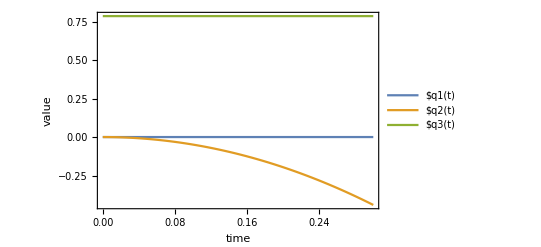

```mathematica
(* Plot *)
qsPlot=Table[Piecewise[qsvars[[i]]/.data],{i,1,nVars}];
Show[Plot[Evaluate[qsPlot],{t,0,end},PlotLegends->qs,
	PlotRange->Automatic,Frame->True,FrameLabel->{"time","value"}]]
```

```mathematica
plotGetLinkCoords[T_,l_]:=Module[{pFront,pBack},
p0x=T[[1,4]];
p0y=T[[2,4]];
pFront=T.Transpose[{{l/2,0,0,1}}]//Simplify;
pBack=T.Transpose[{{-l/2,0,0,1}}]//Simplify;
Line[{pFront[[1;;2,1]],pBack[[1;;2,1]]}]
]
links=Table[plotGetLinkCoords[Ts[[i]],lens[[i]]],{i,1,nObjects}];
```

```mathematica
(* Animate *)
(*linksCoords[i_]:=(links[[i]]/.sim)[[1]];*)
linksCoords[j_]:=links[[j]]/.Table[qs[[i]]->qsPlot[[i]],{i,1,nVars}];
LinksForAnimation[tt_]:=(Table[linksCoords[i],{i,1,Length[links]}])/.t->tt;
Animate[Show[
{Graphics[LinksForAnimation[t]]
},PlotRange-> {{-2,2},{-2,2}},Frame-> True],{t,0,timeend}]
```